## Execute this

### Loading

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
polar1bt=Import["data/polarValArray_b2t.mx"];
polar1tb=Import["data/polarValArray_t2b.mx"];
nematic1bt=Import["data/nematicValArray_b2t.mx"];
nematic1tb=Import["data/nematicValArray_t2b.mx"];
```

```mathematica
Table[polar1bt[[;;,i,1]]=Range[0,0.75,0.03]/0.12;,{i,Length@polar1bt[[1]]}];
Table[polar1tb[[;;,i,1]]=Range[0,0.75,0.03]/0.12;,{i,Length@polar1tb[[1]]}];
Table[nematic1bt[[;;,i,1]]=Range[0,0.75,0.03]/0.12;,{i,Length@nematic1bt[[1]]}];
Table[nematic1tb[[;;,i,1]]=Range[0,0.75,0.03]/0.12;,{i,Length@nematic1tb[[1]]}];
```

```mathematica
phip=polar1bt[[1,;;,2]]*0.12*0.3*180/π;
```

```mathematica
Table[polar1bt[[i,;;,2]]=phip;,{i,Length@polar1bt}];
Table[polar1tb[[i,;;,2]]=phip;,{i,Length@polar1tb}];
Table[nematic1bt[[i,;;,2]]=phip;,{i,Length@nematic1bt}];
Table[nematic1tb[[i,;;,2]]=phip;,{i,Length@nematic1tb}];
```

```mathematica
deltaPphip=Flatten[polar1bt,1];
tempPLUS=Flatten[polar1bt,1];
tempMINUS=Flatten[polar1tb,1];
Table[deltaPphip[[i,3]]=tempPLUS[[i,3]]-tempMINUS[[i,3]],{i,1,Length@deltaPphip}];
```

### Plotting

individual sweeps

```mathematica
min=-0.0;
max=1.0;
colormap={"DeepSeaColors","Reverse"};
colfunc=ColorData[colormap][#/max]&;
legPPLUS=BarLegend[{colfunc,{min,max}},LegendLabel->"P_+"];
legPMINUS=BarLegend[{colfunc,{min,max}},LegendLabel->"P_-"];
legNPLUS=BarLegend[{colfunc,{min,max}},LegendLabel->"N_+"];
legNMINUS=BarLegend[{colfunc,{min,max}},LegendLabel->"N_-"];
polplotbt=ListDensityPlot[Flatten[polar1bt,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->legPPLUS,FrameLabel->{"α","φ_p"}];
polplottb=ListDensityPlot[Flatten[polar1tb,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->legPMINUS,FrameLabel->{"α","φ_p"}];
nemplotbt=ListDensityPlot[Flatten[nematic1bt,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->legNPLUS,FrameLabel->{"α","φ_p"}];
nemplottb=ListDensityPlot[Flatten[nematic1tb,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->legNMINUS,FrameLabel->{"α","φ_p"}];
GraphicsRow[{polplotbt,polplottb},ImageSize->600]
GraphicsRow[{nemplotbt,nemplottb},ImageSize->600]
```

-Graphics-

-Graphics-

hysteresis

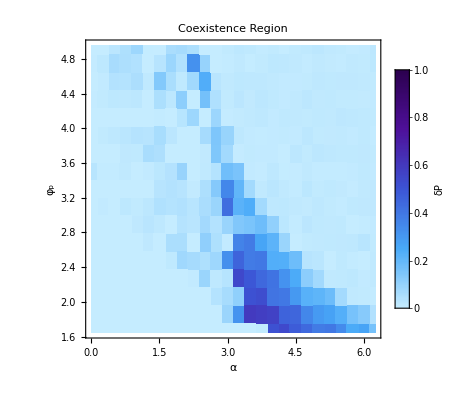

```mathematica
min=-0.01;
max=1.;
colormap={"DeepSeaColors","Reverse"};
colfunc=ColorData[colormap][#/max]&;
leg=BarLegend[{colfunc,{min,max}},LegendLabel->"δP"];
ListDensityPlot[deltaPphip,InterpolationOrder->0,PlotLabel->Style["Coexistence Region",14],PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->leg,FrameLabel->{"α","φ_p"}]
```